### Day 1 “Chronal Calibration”

Part 1 Answer: 543

Part 2 Answer: 621

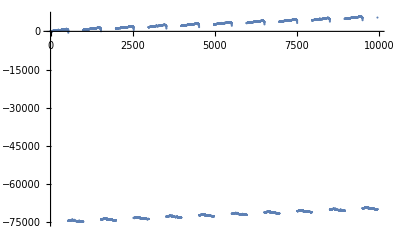

```mathematica
frequencyChanges=
ToExpression[
ReadList[
OpenRead[
StringJoin[NotebookDirectory[] ,"day1.txt"]]]];
Print["Part 1 Answer: ",Total[frequencyChanges]]
firstRepeated=Catch@Module[{frequency=0,seen=<||>},
While[True,
Do[
frequency+=f;
If[KeyExistsQ[seen,frequency],Throw[frequency],seen[frequency]=1],
{f,frequencyChanges}]]];
Print["Part 2 Answer: ",firstRepeated]
frequencyChangesRepeated=PadRight[frequencyChanges,10*Length[frequencyChanges],frequencyChanges];
frequencies=Accumulate[frequencyChangesRepeated];
ListPlot[frequencies]
```

### Day 2 “Inventory Management System”

```mathematica
fileInput=OpenRead["/Users/dmitron/Downloads/AdventOfCode/day2.txt"];
ids=ToString/@ReadList[fileInput];
ContainsXQ[id_,X_]:=MemberQ[(id//Characters//Tally//Transpose)[[2]],X];
twos=Select[ids,ContainsXQ[#,2]&]//Length;
threes=Select[ids,ContainsXQ[#,3]&]//Length;
Print["Part 1 Answer: ",twos*threes]
{id1,id2}=Catch@Block[{},
Do[
If[HammingDistance[x[[1]],x[[2]]]==1,Throw[x]],{x,Tuples[ids,2]}]];
lettersInCommon=Map[#[[1]]&,Select[({id1//Characters,id2//Characters}//Transpose),#[[1]]==#[[2]]&]]//StringJoin;
Print["Part 2 Answer: ", lettersInCommon]
```

Part 1 Answer: 6175

Part 2 Answer: asgwjcmzredihqoutcylvzinx

### Day 3 “No Matter How You Slice It”

```mathematica
claims=Import["/Users/dmitron/Downloads/AdventOfCode/day3.txt","List"];
processedClaims=Map[StringCases[#,RegularExpression["\\d+"]]&,claims]//ToExpression;
fabric=ConstantArray[0,{1000,1000}];
Scan[
fabric[[
#[[2]]+1;;#[[2]]+#[[4]],
#[[3]]+1;;#[[3]]+#[[5]] ]]+=1&,processedClaims];
overlappingArea=(fabric//Flatten//Tally//Transpose)[[2,3;;]]//Total;
Print["Part 1 Answer: ",overlappingArea]
ClaimAloneQ[claim_]:=AllTrue[fabric[[
claim[[2]]+1;;claim[[2]]+claim[[4]],
claim[[3]]+1;;claim[[3]]+claim[[5]]]]//Flatten ,#==1&]
claimID=FirstPosition[Map[ClaimAloneQ,processedClaims],True]//First;
Print["Part 2 Answer: ",claimID]
```

Part 1 Answer: 119551

Part 2 Answer: 1124

### Day 4 “Repose Record”

```mathematica
input=Import["/Users/dmitron/Downloads/AdventOfCode/day4.txt","List"];
log=Join@@StringCases[input,"["~~ts:__~~"] "~~evt:__:>{DateObject[ts],evt}];
sortedLog=Sort[log];
sleepRecord=<||>;
Module[{currentRecord,guard,time,message},
Do[
{time,message}=event;
Switch[message,
"falls asleep",
(currentRecord[[DateValue[time,"Minute"]+1]]+=1;
sleepRecord[guard]=currentRecord),
"wakes up",
(currentRecord[[DateValue[time,"Minute"]+1]]-=1;
sleepRecord[guard]=currentRecord),
_,
(guard=ToExpression@First@StringCases[message,NumberString];
currentRecord=Lookup[sleepRecord,guard,ConstantArray[0,60]])],
{event,sortedLog}]];
Do[sleepRecord[guard]=Accumulate[sleepRecord[guard]],{guard,Keys[sleepRecord]}];
guardMostAsleep=Last@Keys@Sort[Total/@sleepRecord];
minuteMostAsleep=First@Ordering[sleepRecord[guardMostAsleep],-1]-1;
guardModeAsleep=Last@Keys@Sort[Max/@sleepRecord];
minuteModeAsleep=First@Ordering[sleepRecord[guardModeAsleep],-1]-1;
Print["Part 1 Answer: ",guardMostAsleep*minuteMostAsleep]
Print["Part 2 Answer: ",guardModeAsleep*minuteModeAsleep]
```

Part 1 Answer: 95199

Part 2 Answer: 7887

### Day 5 “Alchemical Reduction”

```mathematica
adventString=Import["/Users/dmitron/Downloads/AdventOfCode/day5.txt","String"];
ReactString[string_]:=Module[
{mappings=Map[RegularExpression[#]->""&,Join[Map[StringJoin[#,ToUpperCase[#]]&,CharacterRange["a","z"]],
Map[StringJoin[#,ToLowerCase[#]]&,CharacterRange["A","Z"]]]]},
FixedPoint[StringReplace[#,mappings]&,string]
]
Print["Part 1 Answer: ",StringLength@ReactString[adventString]]
t=Map[
StringLength@ReactString@StringReplace[adventString,{#->"",ToUpperCase[#]->""}]&,CharacterRange["a","z"]];
Print["Part 2 Answer: ",Min[t]]
```

Part 1 Answer: 11755

Part 2 Answer: 4099

Group Theory Solution (Failed Attempt)

```mathematica
fileOpen=OpenRead["/Users/dmitron/Downloads/AdventOfCode/day5.txt"];
adventString=ReadLine[fileOpen];
adventString=StringDrop[StringDrop[StringReplace[adventString,""->"^"],1],-1];
f[string_,i_]:=StringReplace[string,ToString[i]->StringJoin["Log[",ToLowerCase[i],",1]"]];
adventString=f[adventString,"L"];
```

### Day 6 “Chronal Coordinates”

```mathematica
coordinates=Import["/Users/dmitron/Downloads/AdventOfCode/day6.txt","Data"];
{minX,maxX}=MinMax[(coordinates//Transpose)[[1]]];
{minY,maxY}=MinMax[(coordinates//Transpose)[[2]]];
distanceMatrix=Table[
ManhattanDistance[{i,j},coordinates[[k]]],{k,1,50},{i,1,maxX},{j,1,maxY}];
minDistance=Table[Min[distanceMatrix[[;;,i,j]]],{i,1,maxX},{j,1,maxY}];
AssignOwner[i_,j_]:=Module[{},
distances=distanceMatrix[[;;,i,j]];
minDistance2=Min[distances];
If[Count[distances,minDistance2]==1,
Position[distances,minDistance2][[1,1]],-1
]];
regionOwner=Table[AssignOwner[i,j]
,{i,1,maxX},{j,1,maxY}];
infiniteOwners=Catenate[{regionOwner[[1,;;]],
regionOwner[[;;,1]],
regionOwner[[-1,;;]],
regionOwner[[;;,-1]]}]//DeleteDuplicates;
largestOwner=Sort[(Fold[DeleteCases[#1,#2]&,Flatten[regionOwner],infiniteOwners]//Tally),#1[[2]]>#2[[2]]&][[1,1]];
Print["Part 1 Answer: ",largestOwner]
totalDistances=Total[distanceMatrix];
areaLessThan10k=Select[totalDistances//Flatten,#<10000&]//Length;
Print["Part 2 Answer: ",areaLessThan10k]
```

Part 1 Answer: 28

Part 2 Answer: 40244

```mathematica
padding={{30,30},{30,30}};
p1=ArrayPlot[distanceMatrix[[10]],PlotLabel->"10th Coordinate Distance Function",ImagePadding->padding];
p2=ArrayPlot[minDistance,PlotLabel->"Min Distance To Nearest Point",ImagePadding->padding];
p3=ArrayPlot[regionOwner,PlotLabel->"Space Colored By Owner",ImagePadding->padding];
GraphicsGrid[{{p1},{p2},{p3}},ImageSize->500]
```

-Graphics-

```mathematica
coordinates={{1,1},{19,1},{20,20},{1,19},{19,19}}
{minX,maxX}=MinMax[(coordinates//Transpose)[[1]]];
{minY,maxY}=MinMax[(coordinates//Transpose)[[2]]];
distanceMatrix=Table[
ManhattanDistance[{i,j},coordinates[[k]]],{k,1,5},{i,1,maxX},{j,1,maxY}];
minDistance=Table[Min[distanceMatrix[[;;,i,j]]],{i,1,maxX},{j,1,maxY}];
AssignOwner[i_,j_]:=Module[{},
distances=distanceMatrix[[;;,i,j]];
minDistance2=Min[distances];
If[Count[distances,minDistance2]==1,
Position[distances,minDistance2][[1,1]],-1
]];
regionOwner=Table[AssignOwner[i,j]
,{i,1,maxX},{j,1,maxY}];
infiniteOwners=Catenate[{regionOwner[[1,;;]],
regionOwner[[;;,1]],
regionOwner[[-1,;;]],
regionOwner[[;;,-1]]}]//DeleteDuplicates;
largestOwner=Sort[(Fold[DeleteCases[#1,#2]&,Flatten[regionOwner],infiniteOwners]//Tally),#1[[2]]>#2[[2]]&][[1,1]];
Print["Part 1 Answer: ",largestOwner]
totalDistances=Total[distanceMatrix];
areaLessThan10k=Select[totalDistances//Flatten,#<10000&]//Length;
Print["Part 2 Answer: ",areaLessThan10k]
padding={{30,30},{30,30}};
p1=ArrayPlot[distanceMatrix[[3]],PlotLabel->"10th Coordinate Distance Function",ImagePadding->padding];
p2=ArrayPlot[minDistance,PlotLabel->"Min Distance To Nearest Point",ImagePadding->padding];
p3=ArrayPlot[regionOwner,PlotLabel->"Space Colored By Owner",ImagePadding->padding];
GraphicsGrid[{{p1},{p2},{p3}},ImageSize->500]
```

{{1,1},{19,1},{20,20},{1,19},{19,19}}

Part 1 Answer: 5

Part 2 Answer: 400

-Graphics-

```mathematica
res=Nearest[coordinates,Join@@Table[{i,j},{i,minX,maxX},{j,minY,maxY}],DistanceFunction->ManhattanDistance];
Last@First@MaximalBy[Tally@Select[res,Length[#]==1&],Last]
distanceMatrix=DistanceMatrix[coordinates,Join@@Table[{i,j},{i,minX,maxX},{j,minY,maxY}],DistanceFunction->ManhattanDistance];
Count[Total[distanceMatrix,{1}],d_ /; d<10000]
```

90

400

```mathematica
Tally@Select[res,Length[#]==1&]
```

{{{{1,1}},81},{{{1,19}},90},{{{19,1}},90},{{{19,19}},81},{{{20,20}},1}}

### Day 7 “The Sum of Its Parts” aka THE WORST

```mathematica
instructions=Import["/Users/dmitron/Downloads/AdventOfCode/day7.txt","List"];
relations=Join@@StringCases[instructions,"Step "~~r1:_~~" "~~ __ ~~ "step " ~~ r2:_  :>{r1,r2}];
dependencies=<||>;

Do[
dependency=Select[relations,#[[2]]==x&];
dependencies[x]=If[Length[dependency]==0,
{},
First@Transpose@dependency],{x,CharacterRange["A","Z"]}];

GetAvailableTasks[doneTasks_]:=Module[{dependencies2=dependencies},
dependencies2=KeyDropFrom[dependencies2,doneTasks];
Do[
dependencies2[x]=
Select[dependencies2[x],Not@MemberQ[doneTasks,#]&],{x,Keys[dependencies2]}];
Sort@Keys@Select[dependencies2,#=={}&]];
CompleteTask[doneTasks_]:=Catenate[{doneTasks,{First@GetAvailableTasks[doneTasks]}}];

Nest[CompleteTask,{},26]//StringJoin
```

BHRTWCYSELPUVZAOIJKGMFQDXN

```mathematica
workerNumber=5;
scheduleState=<|"workerData"->Table[{0,{},{}},{i,workerNumber}],
"doneTasks"->{}|>;
GetAvailableTasks[doneTasks_,currentTasks_]:=Module[{},
Complement[GetAvailableTasks[doneTasks],currentTasks]];
GetScheduleAvailableTasks[scheduleState_]:=Module[{},
currentTasks=scheduleState["workerData"][[;;,2]]//Flatten;
availableTasks=GetAvailableTasks[scheduleState["doneTasks"],currentTasks];
availableTasks
]
UpdateScheduleAvailableTasks[]:=Module[{},
availableTasks=GetScheduleAvailableTasks[scheduleState];
workerData=scheduleState["workerData"];
Scan[(workerData[[#,3]]=availableTasks)&,Range[workerNumber]];
scheduleState["workerData"]=workerData;
]
UpdateScheduleAvailableTasks[];
scheduleState["workerData"];
DoWorkLoop[]:=Module[{},
workerData=scheduleState["workerData"];
doneTasks=scheduleState["doneTasks"];
workerOrder=Ordering[workerData[[All,1]]];
i=1;
While[True,
currentWorker=workerOrder[[i]];
If[workerData[[currentWorker,2]]≠{}&&workerData[[currentWorker,3]]≠{},
(AppendTo[doneTasks,workerData[[currentWorker,2,1]]];
workerData[[currentWorker,2]]={First@workerData[[currentWorker,3]]};
workerData[[currentWorker,1]]+=60+LetterNumber[workerData[[currentWorker,2,1]]];
scheduleState["doneTasks"]=doneTasks;
scheduleState["workerData"]=workerData;
UpdateScheduleAvailableTasks[];
Return[];
)];
If[workerData[[currentWorker,2]]≠{}&&workerData[[currentWorker,3]]=={},
(AppendTo[doneTasks,workerData[[currentWorker,2,1]]];
scheduleState["doneTasks"]=doneTasks;
UpdateScheduleAvailableTasks[];
If[workerData[[currentWorker,3]]=={},
(workerData[[currentWorker,2]]={};
scheduleState["workerData"]=workerData;
UpdateScheduleAvailableTasks[];
Return[]),
(workerData[[currentWorker,2]]={First@workerData[[currentWorker,3]]};
workerData[[currentWorker,1]]+=60+LetterNumber[workerData[[currentWorker,2,1]]];
scheduleState["doneTasks"]=doneTasks;
scheduleState["workerData"]=workerData;
UpdateScheduleAvailableTasks[];
Return[];)];)];
If[workerData[[currentWorker,2]]=={}&&workerData[[currentWorker,3]]≠{},
(workerData[[currentWorker,2]]={First@workerData[[currentWorker,3]]};
workerData[[currentWorker,1]]+=60+LetterNumber[workerData[[currentWorker,2,1]]];
scheduleState["workerData"]=workerData;
UpdateScheduleAvailableTasks[];
Return[];
)];
If[workerData[[currentWorker,2]]=={}&&workerData[[currentWorker,3]]=={},
(i++;
workerData[[currentWorker,1]]=First@First@Select[workerData[[workerOrder]],#[[2]]≠{}&];
scheduleState["workerData"]=workerData;
)];
]
]
Scan[DoWorkLoop[]&,Range[37]]
scheduleState
```

<|workerData→{{959,{},{}},{959,{},{}},{959,{},{}},{959,{},{}},{959,{},{}}},doneTasks→{B,H,R,T,W,Y,Z,C,S,A,E,L,P,U,V,O,I,M,J,K,F,G,Q,D,X,N}|>

### Day 8 “Memory Maneuver”

This was my initial approach which was a simple stack-based approach.

```mathematica
input=ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day8.txt"],Number];
chars=CharacterRange["A","Z"];
testinput="2 3 0 3 10 11 12 1 1 0 1 99 2 1 1 2";
testinput=(StringSplit[testinput," "]//ToExpression);
Do2[input_]:=Module[{},
stack={};
readIndex=1;
metaData={};
Catch@While[True,
If[stack=={},
(If[readIndex≥Length[input],
Throw["done"],
(nextTuple=input[[readIndex;;readIndex+1]];
AppendTo[stack,nextTuple];
readIndex+=2;
)];),
(If[stack[[-1,1]]>0,
(stack[[-1,1]]-=1;
nextTuple=input[[readIndex;;readIndex+1]];
AppendTo[stack,nextTuple];
readIndex+=2;
),
AppendTo[metaData,input[[readIndex;;readIndex+stack[[-1,2]]-1]]];
readIndex+=stack[[-1,2]];
stack=stack[[1;;-2]];
])
]];
metaData//Flatten//Total
]
Do2[input]
Do2[testinput]
```

49602

138

Then I got a hint that recursive structures are excellent for trees. So I started trying to write a recursive parser. It is really confusing to think about.

```mathematica
ScanInput[input_,n_]:=Module[{},
{read,input0}=TakeDrop[input,n];
{read,input0}]
```

Here is a really clever structure that bundles the input into the function. That way, you can simply keep calling the same function and read further in a list. This is a neat kind of stream structure.

```mathematica
StreamReader[input0_]:=Module[{input=input0,read},
Function[n,{read,input}=TakeDrop[input,n];read]];
```

So here is the recursive function. It turned out to be simpler to make this thing argumentless - then you can do the NestList function without worrying about the returns matching up (if you want it not to be argumentless, I think you have to return {children, data, input}, but if you feed that into NestList, it will throw away all the other data; you have two options: create an array that keeps all the data including input at each stage or make it a function with side-effects).

```mathematica
Do3[]:=Module[{read,data,children,nchildren,ndata},
{read,input}=ScanInput[input,2];
nchildren=read[[1]];
ndata=read[[2]];
children=NestList[Do3[]&,Nothing,nchildren];
{data,input}=ScanInput[input,ndata];
If[nchildren>0,
Total[children[[Select[data,#≤ nchildren&]]]],
Total[data]]
]
```

```mathematica
Do4[]:=Module[{read,data,children,nchildren,ndata},
{read,input}=ScanInput[input,2];
nchildren=read[[1]];
ndata=read[[2]];
children=NestList[Do4[]&,Nothing,nchildren];
{data,input}=ScanInput[input,ndata];
Total[data]+Total[children]
]
```

```mathematica
f[a_]:={Total[Range[a]],Total[Range[2 a]]};
g=f[#][[1]]&;
g[4]
NestList[f[#][[1]]&,2,5]
```

```mathematica
input=ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day8.txt"],Number];
Print["Part 1 Answer: ", Do4[]]
input=ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day8.txt"],Number];
Print["Part 2 Answer: ", Do3[]]
```

Part 1 Answer: 49602

Part 2 Answer: 25656

### Day 9 “Marble Mania”

I did part 1, which was pretty natural, but part 2 requires me to speed up the code. I’m pretty sure that the slowest part of the code is the Deletion/Insertion into the board. The board size grows linearly with the number of rounds played and each board change loop requires an O(n) operation, so I’m pretty sure I’m at O(n^2) (let’s see if you have n many board changes and each of those is O(n) operation, then yes). Hence, yea, when I move to n=10^7, this gets seriously out of hand. Anyway, there’s a way to implement a linked list in Mathematica, which I started below, but I got incredible bored, so I stopped. http://www.mathprogramming-intro.org/book/node525.html. I have to implement insert and delete on those structures and man, just nah.

```mathematica
board={0,1};
round=2;
currentMarbleIndex=2;
numPlayers=413;
score=ConstantArray[0,numPlayers];
currentPlayer=2;
lastScore={0,0};
gameState=<|"board"->board,
"round"->round,
"currentMarbleIndex"->currentMarbleIndex,
"numPlayers"->numPlayers,
"score"->score,
"currentPlayer"->currentPlayer,
"lastScore"->lastScore|>;

Non23UpdateRule[gameState_]:=Module[{nextGameState,board,round,currentMarbleIndex,numPlayers,score,currentPlayer},
board=gameState["board"];
round=gameState["round"];
currentMarbleIndex=gameState["currentMarbleIndex"];
numPlayers=gameState["numPlayers"];
score=gameState["score"];
currentPlayer=gameState["currentPlayer"];

currentMarbleIndex=Mod[currentMarbleIndex+2,Length[board],1];
board=Insert[board,round,currentMarbleIndex];
round++;
currentPlayer=Mod[currentPlayer+1,numPlayers,1];

nextGameState=<|"board"->board,
"round"->round,
"currentMarbleIndex"->currentMarbleIndex,
"numPlayers"->numPlayers,
"score"->score,
"currentPlayer"->currentPlayer,
"lastScore"->{0,0}|>;
nextGameState
];
Yon23UpdateRule[gameState_]:=Module[{nextGameState,marble7Index,marblePoints,board,round,currentMarbleIndex,numPlayers,score,currentPlayer,lastScore},
board=gameState["board"];
round=gameState["round"];
currentMarbleIndex=gameState["currentMarbleIndex"];
numPlayers=gameState["numPlayers"];
score=gameState["score"];
currentPlayer=gameState["currentPlayer"];

marble7Index=Mod[currentMarbleIndex-7,Length[board],1];
score[[currentPlayer]]+=round+board[[marble7Index]];
lastScore={round,board[[marble7Index]]};
marblePoints={round,board[[marble7Index]]};
board=Delete[board,marble7Index];
currentMarbleIndex=Mod[marble7Index,Length[board],1];
round++;
currentPlayer=Mod[currentPlayer+1,numPlayers,1];

nextGameState=<|"board"->board,
"round"->round,
"currentMarbleIndex"->currentMarbleIndex,
"numPlayers"->numPlayers,
"score"->score,
"currentPlayer"->currentPlayer,
"lastScore"->lastScore|>;
nextGameState
];
UpdateRule[gameState_]:=Module[{nextGameState},
If[Mod[gameState["round"],23]==0,
nextGameState=Yon23UpdateRule[gameState],
nextGameState=Non23UpdateRule[gameState]];
nextGameState];
Nest[UpdateRule,gameState,71082]["score"]//Max
```

416424

```mathematica
toLinkedList[x_List]:=Fold[{#2,#1}&,{},Reverse[x]];
```

```mathematica
gameState["board"]
```

{0,1}

```mathematica
ll=toLinkedList[RandomReal[1,100]];
```

```mathematica
popFromLinkedList[x_List]:=;
```

```mathematica
deleteFromLinkedList[x_List,ix_]:=
```

```mathematica
ConstantArray[2,1]
```

{2}

```mathematica
ConstantArray[2,3]//Flatten
```

{2,2,2}

```mathematica
ll[[ConstantArray[2,4]]]
```

{{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}},{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}},{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}},{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

```mathematica
ll
```

{0.282863,{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

```mathematica
ll[[2]]=ll[[2,2]]
```

{0.321568,{0.156196,{0.888116,{0.57331,{0.011184,{0.228497,{0.836493,{0.324202,{0.446396,{0.099615,{0.831627,{0.813457,{0.772651,{0.230156,{0.92111,{0.011576,{0.229745,{0.926777,{0.272229,{0.268621,{0.304079,{0.445686,{0.955838,{0.597644,{0.683878,{0.743853,{0.213873,{0.326876,{0.576176,{0.725486,{0.847337,{0.805494,{0.670234,{0.929408,{0.694424,{0.117784,{0.852901,{0.0218667,{0.958206,{0.199143,{0.348163,{0.522998,{0.711081,{0.846813,{0.600804,{0.764063,{0.0924788,{0.613192,{0.0131891,{0.362299,{0.0701099,{0.0524749,{0.564257,{0.287738,{0.726197,{0.234204,{0.493119,{0.975585,{0.80678,{0.333918,{0.154574,{0.342606,{0.849424,{0.926786,{0.961002,{0.941545,{0.779298,{0.266867,{0.22069,{0.185158,{0.18265,{0.923759,{0.11578,{0.482396,{0.349335,{0.130427,{0.430376,{0.432452,{0.277872,{0.79629,{0.47229,{0.0428771,{0.479619,{0.619949,{0.54314,{0.909956,{0.696841,{0.674518,{0.182979,{0.947521,{0.924053,{0.164061,{0.016354,{0.331148,{0.719888,{0.16139,{0.00821481,{}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

### Day 10 “The Stars Align”

```mathematica
s=Map[StringCases[#,RegularExpression["-?[0-9]+"]]&,
ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day10.txt"],String]]//ToExpression;
s[[;;,2]]=-s[[;;,2]];
s[[;;,4]]=-s[[;;,4]];
```

```mathematica
pos[t_]:=s[[;;,1;;2]]+t*s[[;;,3;;4]];
ns=N[s];
npos[t_]:=ns[[;;,1;;2]]+t*s[[;;,3;;4]];
```

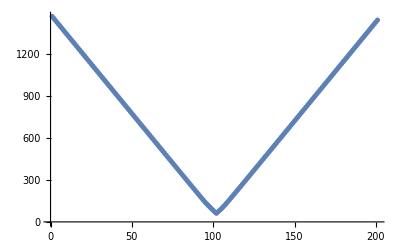

```mathematica
ListPlot[Table[Max[DistanceMatrix[npos[t]]],{t,10000,10200}]]
```

```mathematica
m=Min[Table[Max[DistanceMatrix[npos[t]]],{t,10000,10200}]];
10000+First@FirstPosition[Table[Max[DistanceMatrix[npos[t]]],{t,10000,10200}],m]-1
```

10101

```mathematica
t=10101;
{xmin,xmax}=MinMax[pos[0][[;;,1]]];
{ymin,ymax}=MinMax[pos[0][[;;,2]]];
```

```mathematica
ArrayPlot[SparseArray[Map[#->1&,pos[t]]]]
```

-Graphics-

### Day 11 “Chronal Charge”

Puzzle input 2866.

```mathematica
input=2866;
fuelCells=Table[{i,j},{i,1,300},{j,1,300}];
GetCellPowerLevel[i_,j_,serialNumber_]:=Quotient[
Mod[((i+10)*j+serialNumber)*(i+10),1000]
,100]-5;
GetCellPowerLevel[i_,j_]:=GetCellPowerLevel[i,j,input];
fuelCellValues=Table[GetCellPowerLevel[i,j],{i,1,300},{j,1,300}];
GetRegionPowerLevel[i_,j_,size_]:=Total@Flatten[fuelCellValues[[i;;i+size-1,j;;j+size-1]]];
GetGridPowerLevel[size_]:=Module[{},
Table[GetRegionPowerLevel[i,j,size],{i,1,300-size},{j,1,300-size}]
];
```

```mathematica
Max[GetGridPowerLevel[3]]
Position[GetGridPowerLevel[3],Max[GetGridPowerLevel[3]]]
```

30

{{20,50}}

```mathematica
s=Table[Max[GetGridPowerLevel[size]],{size,5,12}]
```

{54,57,77,73,88,79,78,64}

```mathematica
Max[GetGridPowerLevel[9]]
Position[GetGridPowerLevel[9],Max[GetGridPowerLevel[9]]]
```

88

{{238,278}}

### Day 12 “Subterranean Sustainability”

```mathematica
input=ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day12.txt"],String];
input=StringSplit[
StringReplace[input,{"#"->"1","."->"0"}], " "];
initialState=ToExpression@Characters[input[[1]]][[3]];
rules=Map[ToExpression@Characters[#[[1]]]->ToExpression@Characters[#[[3]]][[1]]&,input[[2;;]]];
generations=20;
pad=generations+5;
ca=CellularAutomaton[rules,ArrayPad[initialState,pad],{{generations}}];
ca[[-1]].Range[0-pad,Length[initialState]-1+pad]
```

1184

```mathematica
ArrayPlot@(CellularAutomaton[rules,ArrayPad[initialState,145],{140}])
```

-Graphics-

```mathematica
Flatten[Position[CellularAutomaton[rules,ArrayPad[initialState,145],{140}][[-1]],1]-141]//Total
```

944

```mathematica
generations=145;
pad=generations+5;
ca=CellularAutomaton[rules,ArrayPad[initialState,pad],{{generations}}];
ca[[-1]].Range[0-pad,Length[initialState]-1+pad]
```

944

```mathematica
944-5*145
```

219

```mathematica
GetValue[generation_]:=5*generation+219;
```

```mathematica
GetValue[50000000000]
```

250000000219

### Day 13 “Mine Cart Madness”

Got pretty close with this one. I don’t recall where I stopped, but I think I was just about ready to run it on the full input.

```mathematica
input=Map[Characters,ReadList[OpenRead["/Users/dmitron/Downloads/AdventOfCode/day13.txt"],String]];
input//MatrixForm
carts=Join[
Map[{Pos2Complex@PosT[#],1,0}&,Position[input,">"]],
Map[{Pos2Complex@PosT[#],-1,0}&,Position[input,"<"]],
Map[{Pos2Complex@PosT[#],I,0}&,Position[input,"^"]],
Map[{Pos2Complex@PosT[#],-I,0}&,Position[input,"v"]]
];
Pos2Complex[pos_]:=pos[[1]]+pos[[2]]I;
Complex2Pos[comp_]:={Re[comp],Im[comp]};
PosT[pos_]:={pos[[2]],7-pos[[1]]};
IPosT[pos_]:={-pos[[2]]+7,pos[[1]]};
Complex2Pos@Pos2Complex[{x,y}]
IPosT@PosT[{x,y}]
input=input/.{">"->"-","<"->"-","v"->"|","^"->"|"};
input//MatrixForm
Turn[n_]:=Module[{out},
If[Mod[n,3]==0,
out=I];
If[Mod[n,3]==1,
out=1];
If[Mod[n,3]==2,
out=-I];
out];
UpdateCart[cart_]:=Module[{newCart=cart},
{x,y}=IPosT@Complex2Pos[cart[[1]]+cart[[2]]];
nextChar=input[[x,y]];
If[nextChar=="/"&&cart[[2]]==1,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=I*cart[[2]])];
If[nextChar=="/"&&cart[[2]]==-I,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=-I*cart[[2]])];
If[nextChar=="/"&&cart[[2]]==-1,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=I*cart[[2]])];
If[nextChar=="/"&&cart[[2]]==I,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=-I*cart[[2]])];
If[nextChar=="\\"&&cart[[2]]==1,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=-I*cart[[2]])];
If[nextChar=="\\"&&cart[[2]]==-I,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=I*cart[[2]])];
If[nextChar=="\\"&&cart[[2]]==-1,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=-I*cart[[2]])];
If[nextChar=="\\"&&cart[[2]]==I,
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=I*cart[[2]])];
If[nextChar=="+",
(newCart[[1]]=cart[[1]]+cart[[2]];
newCart[[2]]=cart[[2]]*Turn[cart[[3]]];
newCart[[3]]++)];
If[nextChar=="-",
newCart[[1]]=cart[[1]]+cart[[2]]];
If[nextChar=="|",
newCart[[1]]=cart[[1]]+cart[[2]]];
newCart
];
CrashLocation[carts_]:=Module[{},
locations=Tally[carts[[;;,1]]];
Select[Tally[carts[[;;,1]]],#[[2]]==2&]
];
PerformLoop[carts_]:=Module[{newCarts=carts,crash},
crash=False;
Do[
newCarts[[i]]=UpdateCart[newCarts[[i]]];
If[CrashLocation[newCarts]≠{},
crash=True;
Break[]],
{i,Range[Length[carts]]}];
If[crash,
Return[CrashLocation[newCarts]],
Return[newCarts]]
];
PosT2[pos_]:={pos[[1]]-1,6-pos[[2]]};
```

(1)
 |  |  |  |

{4,8}

{4,8}

(1)
 |  |  |  |

```mathematica
PosT2@ReIm@First@First@NestWhile[PerformLoop,carts,Length[#]==2&]
```

{65,4}

```mathematica
ReIm@NestList[PerformLoop,carts,14][[;;,;;,1]];
```

### Day 14 “Chocolate Charts”

This one is done, but the second part never finished even after something like 6 hours of compute time. I think this is another one of those instances where even doing it via Python would speed it up. That’s not fun though.

```mathematica
input=360781;
DoRecipes[input0_,input1_]:=Module[{input=IntegerDigits[input0]},
current1=1;
current2=2;
While[
SequencePosition[input,IntegerDigits[input1]]=={},
input=Join[input,IntegerDigits[input[[current1]]+input[[current2]]]];
current1=Mod[current1+1+input[[current1]],Length[input],1];
current2=Mod[current2+1+input[[current2]],Length[input],1];
];
input
];
recipes=DoRecipes[37,input];
Map[ToString,recipes[[input+1;;input+10]]]//StringJoin
First@First@SequencePosition[recipes,IntegerDigits[input]]-1
```

18